# Quantum Brownian Motion

## References

Path integral approach to quantum Brownian motion, by Caldeira and Leggett

["Reduction of a wave packet in quantum Brownian motion by Unruh and Zurek"](https://journals-aps-org.ezp.sub.su.se/prd/abstract/10.1103/PhysRevD.40.1071)

## Gaussian integral identity

-Graphics-
-Graphics-

## Keldysh path integral for coherent bosons in a single quantum level

See Kamenev’s book, chapter 2 and 3

### Partition function definition

Define:

ρ̂ is an initial density matrix. We will choose it to be in thermal eq:
-Graphics- (notice that it is not normalized to unity)
and the unitary evolution operator:
-Graphics-

The trace is cyclic, and adding an identity operator expanded in a complete basis, i.e. OverHat[1]=∑_(i,j=1)^N |ϕ_i⟩  ⟨ϕ_i|,
and using the trace of a scalar is a scalar, then we have:
	 Tr A B=∑_(i,j=1)^N ⟨ϕ_j|A|ϕ_i⟩⟨ϕ_i|B|ϕ_j⟩

### Example: bosonic particles in a single quantum state with energy ω_0

#### Hamiltonian

Consider:
-Graphics-=ω_0 N̂
then
-Graphics-,-Graphics-

#### Path Integral steps

In order to derive the path integral formulation, let's divide the contour in the following way:
	-Graphics-

First, let's insert the over-complete coherent state basis:
	-Graphics-
at the initial and final states, then commute the integrals with the trace and then use the cyclic property of the trace:
	Tr U_C ρ  = ∫d[(ϕ̄)_1,ϕ_1]∫d[(ϕ̄)_(2N),ϕ_(2N)]ⅇ^(-|ϕ_1|^2-|ϕ_(2N)|^2) ⟨ϕ_1|U_c|ϕ_(2N)⟩    ⟨ϕ_(2N)|ρ|ϕ_1⟩ 

We can insert the over-complete basis at discrete infinitesimal time intervals, in order to derive the path integral:
For example, for N=3:
	-Graphics-
or more generally:
	⟨ϕ_1|(ρ̂)_0|ϕ_(2N)⟩ 
{ ∏_(j=1)^(N-1) ⟨ϕ_(j+1)|(Û)_δ_t|ϕ_j⟩}
⟨ϕ_N|1|ϕ_(N+1)⟩  
{∏_(j=N)^(2N-1) ⟨ϕ_(j+1)|(Û)_-δ_t|ϕ_j⟩}
Up to linear order in δ_t:
	-Graphics-
This actually applies to any normally-ordered H. -> Other examples? 

Use the identity:
	⟨ϕ_1|(ρ̂)_0|ϕ_(2N)⟩=exp{(ϕ̄)_1 ϕ_(2N)ρ(ω_0)}
and that
	-Graphics-
we derive the partition function below.

#### Partition function discrete

-Graphics-
Note that G is non-diagonal, and it depends on the Hamiltonian. 
For N=3:
 -Graphics-, -Graphics-
Its inverse gives the 2-pt correlation functions.

#### 2-pt correlation functions, discrete

-Graphics-
 For N=3, we get
 -Graphics-, ρ=ρ(ω_0)

#### 2-pt correlation functions in the continuum limit: N→ ∞, ϕ_i→ ϕ(t)

Determinant in the continuum limit:
	-Graphics-
2-pt functions (+ and - indicate the positive and the negative branches of the Keldysh contour.):
	-Graphics-
where the bosonic occupation number is:
	-Graphics-

#### Green functions in the continuum limit and Keldysh space

Keldysh rotation:
	-Graphics-
2-pt correlation functions:
	-Graphics-
	-Graphics-
	-Graphics-
Properties 
	-Graphics-

#### Fluctuation-Dissipation Theorem: G^K(ϵ)=Coth[(ω_0-μ)/(2 T)](G^R(ϵ)-G^A(ϵ))

For a thermal initial state, 
	-Graphics-
and using the delta identity:
	∫_(-∞)^∞ e^(ⅈ ω t)ⅆt = 2 π δ(ω) =ⅈ(1/(ω +ⅈ 0)-1/(ω -ⅈ 0))
	∫_0^∞ e^((ⅈ ω-0) t)ⅆt =ⅈ/(ω +ⅈ 0)
	∫_(-∞)^0 e^((ⅈ ω+0) t)ⅆt =-ⅈ/(ω -ⅈ 0)
we can rewrite:
	G^K(ϵ)=-2π ⅈ (2/(e^((ω_0-μ)/T)-1)+1)δ(ϵ-ω_0)
	=- ⅈ ((e^((ω_0-μ)/T)+1)/(e^((ω_0-μ)/T)-1))ⅈ(1/(ϵ-ω_0 +ⅈ 0)-1/(ϵ-ω_0 -ⅈ 0))
	=Coth[(ω_0-μ)/(2 T)](G^R(ϵ)-G^A(ϵ))
which is the FDT and it holds in general.

#### Nonlinear Fluctuation-Dissipation Theorem

Higher order correlation functions in Keldysh space are not all independent of each other, just like in the 2-pt case. See:

[A Generalized Fluctuation-Dissipation Theorem for NonlinearResponse Functions](https://arxiv.org/pdf/hep-th/9809016.pdf)

#### Partition function in the continuum limit

Partition function is formally:
	-Graphics-	

The naive way gives a non-interacting action. Taking into account the 2-pt correlation functions: 
	-Graphics-

## Keldysh action for the harmonic oscillator

### Classical action along the Keldysh contour S[X^cl, x^q]=2∫_C dt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q)

Single particle in an arbitrary potential, where C is the Keldysh closed time contour:
-Graphics-
Splitting the contour in the + and - branches:
	S[X_+, x_-]=∫_(-∞)^∞ ⅆt [2(Ẋ)^cl(Ẋ)^q-V(X_+)+V(X_-)]
then do the Keldysh rotation:
-Graphics-
The action becomes ()after a partial integration for the 1st term):
-Graphics-

#### Harmonic oscillator

V(X)=ω_0/2 X^2
S[X^cl, x^q]=2∫_C dt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q)

#### Small X^q expansion

-Graphics-
V’(X) is derivative respective X

### Keldysh action S[X^cl,X^q]=2∫_(-∞)^∞ ⅆt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

The Keldysh action takes into account the 2-pt correlation between the fields of the different branches:
	-Graphics-
	-Graphics-

#### Green functions for the harmonic oscillator

-Graphics-
In Fourier space:
-Graphics-
-Graphics-

#### Action for the harmonic oscillator

D^-1 X=(D^(-1A) X^q, D^(-1R) X^cl+D^(-1K) X^q)
	=2(-(X^(..))^q-ω_0^2 X^q, -(X^(..))^cl-ω_0^2 X^cl+1/2 D^(-1K) X^q)

1/2 X^T D^-1 X =(-X^cl(X^(..))^q-ω_0^2 X^cl X^q-X^q (X^(..))^cl-ω_0^2 X^q X^cl+1/2 X^q D^(-1K) X^q)
		{d/dt(X^cl(Ẋ)^q)=(Ẋ)^cl(Ẋ)^q+X^cl(X^(..))^q, d/dt((Ẋ)^cl X^q)=(Ẋ)^cl(Ẋ)^q+(X^(..))^cl X^q}
                   → 2((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

The last term in red is an additional term that corrects the action if the continuum limit is done naively. It's of higher order in X^q, so it can be ignored in the semiclassical limit.

#### Quartic potential?

V(X) =λ X^4
V(X_+=X^cl+X^q)-V(X_-=X^cl-X^q)=8λ (X^(cl 3)X^q+X^cl X^(q 3))

```mathematica
(xc+xq)^4-(xc-xq)^4//Expand
```

8 xc^3 xq+8 xc xq^3

## Single particle linearly coupled with a bath

### Action

Note that S_p here is the classical action of the single particle! I think the Keldysh action should be used, though in this section, this plays no role.

-Graphics-
σ_1is the Pauli matrix in Keldysh space

### Influence functional

We integrate out S_bath+S_int using a Gaussian integral identity, in order to get the influence functional. Written in the form action, S_diss=ln F, we get:
	-Graphics-	
Note that it is the linear coupling that implies the dissipation action to be quadratic in fields.

Using the results from the single harmonic oscillator in a previous section, we get for the bath:
	-Graphics-
-Graphics-

### Solution for the Ohmic bath

Assuming continuous spectrum for the bath and that it’s ohmic,
	-Graphics-  ≈ -Graphics- (Ohmic bath)

Then we get:
	-Graphics-

#### Ohmic bath computation details

-Graphics-
-Graphics-
-Graphics-
Inverse FT the expression above, we get a non-local expression for the Keldysh component
-Graphics-

Coth[t-τ]

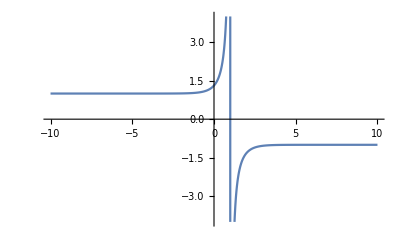

```mathematica
Integrate[1/Sinh[t-τ]^2,τ]
Plot[%/.t->1,{τ,-10,10}]
```

```mathematica
Limit[Coth[x],x->∞]
```

1

## Effective field approach: a free particle interacting with a bath

```mathematica
["Hong-Liu's lecture notes"](https://arxiv.org/pdf/1805.09331.pdf), page 12
```

Note that the particle here is free, namely V(X)=0. However, when the guess the L_EFT, the use general arguments, and do get a term that actually would correspond to the harmonic potential. See more comments below.

```mathematica
-Graphics-
-Graphics-
```

Comparing the above result with the exact result in the previous section, we see that:
	The c x_a x_r term comes from a quadratic potential, but Hong Liu says it’s an effective potential induced by the bath?
	The ν x_a (ẋ)_r and the i/2 σ x_a^2 terms come from integrating out the bath.
	The M̃(ẋ)_a (ẋ)_r term comes from the kinetic term.

Most general terms :
x_a^2 → gives rise the Gaussian noise
x_r^2 → Not there, because of the Lagrangian? ...
x_a x_r
(ẋ)_a x_r → Not there
x_a(ẋ)_r
(ẋ)_a(ẋ)_r

```mathematica
Series[1/(1-x),{x,0,1}]
```

1+x+O[x]^2

### Remark for higher order terms

### Cubic terms

Most general terms :
x_a^3
x_r^3 → should not be there
x_a^2 x_r
x_a x_r^2
((ẋ)_a)^2 x_r
x_a((ẋ)_r)^2
(ẋ)_a x_r^2
x_a^2(ẋ)_r
((ẋ)_a)^2(ẋ)_r
(ẋ)_a((ẋ)_r)^2

### Stochastic equation for some cubic terms such that the noise is Gaussian

Legendre transformation to get the Gaussian noise ξ :

Then, the argument of the exponential is:
	-c x_a x_r -ν x_a (ẋ)_r+M̃(ẋ)_a (ẋ)_r+i/(2σ) ξ^2+ξ x_a
- α x_a x_r^2 - β x_a((ẋ)_r)^2- γ (ẋ)_a x_r^2 
	
For simplicity, we consider non-linear interactions that are linear in x_a, as shown in the line above.
Now, we can derive the SDE:
	c  x_r +ν (ẋ)_r+M̃(x^(..))_r+α x_r^2+β ((ẋ)_r)^2-2γ x_r(ẋ)_r=ξ
What are the meanings of the new terms? Are they physical?

### Non Gaussian noise?

## Linear QBM exact quantum master eq

### Setting

Master equation is the time evolution of the (reduced) density matrix:
-Graphics-
The goal is to find H_ρ operator.

#### Feynman-Vernon

Assuming the initial density matrix can be factorized to the one of the Brownian motion particle, i.e. ρ_r, and that of the bath, 
-Graphics-
then:
-Graphics-
where J_r is an evolution operator, with the path-integral representation:
-Graphics-
F[x,x'] is called the influence functional, which contains the bath dof and the interaction with the bath (it contains the initial bath density matrix too).
The bath's initial density matrix will be assumed to be in thermal eq.

#### Action

-Graphics-

#### Spectral density

The spectral density is defined as:
-Graphics-
We study the ones that have the shape:
-Graphics-

{{√10 ⅇ^(-ω^2/100) √ω,ⅇ^(-ω^2/100) ω,1/100 ⅇ^(-ω^2/100) ω^3}}

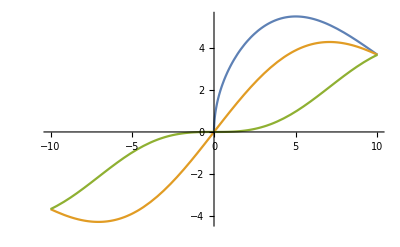

```mathematica
ω (ω/Λ)^{n-1} Exp[-ω^2/Λ^2]/.n->{1/2,1,3}/.Λ->10
Plot[Evaluate@%,{ω,-10,10}]
```

### Influence functional, fluctuation-dissipation

ln F[x,x']=-ⅈ/ħ ∫_0^t ds_1∫_0^s_1 ds_2{x_q(s_1)η(s_1-s_2) x_cl(s_2) -ⅈ x_q(s_1)ν(s_1-s_2) x_q(s_2)}

Noise or fluctuation kernel is non-local in general:
-Graphics-

Dissipation kernel:
-Graphics-
-Graphics-

Fluctuation-dissipation relation:
-Graphics-
Classical or high T limit:
-Graphics-

⋁[ω,s]=I[ω]Coth[1/2 β ℏ ω]Cos[ω s]
K[ω,s]=ω/π Coth[1/2 β ℏ ω]Cos[ω s]
γ[ω,s]=1/ω I[ω]Cos[ω s]

⋁[ω,s]=π K[ω,s]γ[ω,s] /Cos[ω s]
=∫_(-∞)^∞ ⅆs' ∫_0^∞ ⅆω' K[ω,s-s']γ[ω',s']

⋁[s]=∫_(-∞)^∞ ⅆs'  K[s-s']γ[s']
	=∫_(-∞)^∞ ⅆs'∫_0^∞ ⅆω ∫_0^∞ ⅆω' K[ω,s-s']γ[ω',s']
	=∫_(-∞)^∞ ⅆs'∫_0^∞ ⅆω ∫_0^∞ ⅆω' ω/π Coth[1/2 β ℏ ω]Cos[ω (s-s')]1/ω' I[ω']Cos[ω' s']
	=∫_0^∞ ⅆω ∫_0^∞ ⅆω' ω/π Coth[1/2 β ℏ ω]1/ω' I[ω']∫_(-∞)^∞ ⅆs'Cos[ω (s-s')]Cos[ω' s']

```mathematica
Integrate[ω Coth[ω]Cos[ω],ω]//FullSimplify
%/.ω->0
%%/.ω->∞
```

Cos[ω]+1/4 ⅇ^(-ⅈ ω) (HurwitzLerchPhi[ⅇ^(2 ω),2,-ⅈ/2]-4 ⅈ ω Hypergeometric2F1[-ⅈ/2,1,1-ⅈ/2,ⅇ^(2 ω)])+1/4 ⅇ^(ⅈ ω) (HurwitzLerchPhi[ⅇ^(2 ω),2,ⅈ/2]+4 ⅈ ω Hypergeometric2F1[ⅈ/2,1,1+ⅈ/2,ⅇ^(2 ω)])+ω Sin[ω]

Infinity::indet: Indeterminate expression 0 ((-ⅈ) ∞) encountered.

Infinity::indet: Indeterminate expression 0 (ⅈ ∞) encountered.

Indeterminate

Infinity::indet: Indeterminate expression ⅇ^((-ⅈ) ∞) encountered.

Infinity::indet: Indeterminate expression ⅇ^(ⅈ ∞) encountered.

Indeterminate

```mathematica
Integrate[Cos[ω1 (s-t)]Cos[ω2 t],t]
```

```mathematica
-Sin[s ω1+t (-ω1+ω2)]/(2 (ω1-ω2))-Sin[s ω1-t (ω1+ω2)]/(2 (ω1+ω2))//FullSimplify
```

-Sin[s ω1+t (-ω1+ω2)]/(2 (ω1-ω2))-Sin[s ω1-t (ω1+ω2)]/(2 (ω1+ω2))

### Exact quantum master equation

-Graphics-

#### Coefficients

-Graphics-
u and v are classical solutions, see the paper
-Graphics-
-Graphics-

#### High T limit of the coefficients: why doesn’t the 2nd diffusion term go to 0 for ohmic case?

```mathematica
-Graphics--Graphics-
```

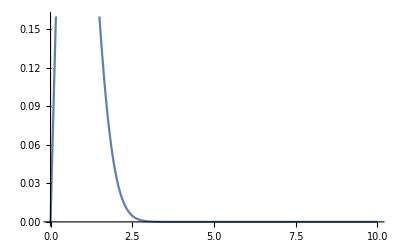

```mathematica
Plot[Λ Exp[-Λ^2],{Λ,0,10}]
```

### Exact Wigner equation

This paper corrects the equation above adding ħ in front of the diffusion coefs.
["https://arxiv.org/pdf/quant-ph/9508004.pdf"](https://arxiv.org/pdf/quant-ph/9508004.pdf)

### Langevin eqs

We use transformations from the Risken book, chapter 3.4. 
In our case the diffusion matrix doesn’t depend on the (q, p).

D_q=p
D_p=-(Ω^2+(δΩ(t))^2) q-Γ(t) p
D_pp=2 ħ Γ(t) h(t)
D_pq=D_qp=-ħ Γ(t) f(t)

q̇= p+√(- ħ Γ(t) f(t))ξ_p
ṗ=-(Ω^2+(δΩ(t))^2)q-Γ(t) p+√(ħ Γ(t) f(t))ξ_p+√(-ħ Γ(t) f(t)) ξ_q

q^(..)= -(Ω^2+(δΩ(t))^2)q
	-Γ(t) (q̇-√(- ħ Γ(t) f(t))ξ_p)
          +√(2ħ Γ(t) h(t))ξ_p+√(-ħ Γ(t) f(t)) (ξ_q+ξ_p)+∂/(∂t)(√(-ħ Γ(t) f(t))ξ_p)
Assume
	q^(..) ≈0
then
Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q
	      + (Γ(t) √(- ħ Γ(t) f(t))+√(2ħ Γ(t) h(t))+√(-ħ Γ(t) f(t))+∂/(∂t)(√(-ħ Γ(t) f(t))))ξ_p
                   +√(-ħ Γ(t) f(t))OverDot[ξ_p]
                   +√(-ħ Γ(t) f(t)) ξ_q

which can be written as
	Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q +√(-ħ Γ(t) f(t))η+√(-ħ Γ(t) f(t)) ξ_q
	          η≡ (Γ(t) +√(-2 h(t)/f(t))+1+(Γ̇(t))/(2 Γ(t))+(ḟ(t))/(2 f(t)))ξ_p+√(-ħ Γ(t) f(t))OverDot[ξ_p]


Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q+ (Γ(t) ϵ+√(2ħ Γ(t) h(t))+ϵ+∂/(∂t)ϵ)ξ_p+ ϵ OverDot[ξ_p]+ ϵ ξ_q

Assume ϵ=√(-ħ Γ(t) f(t)) and ϵ̇=0, then, at leading order
	        η= (Γ(t) +(√(2ħ Γ(t) h(t)))/ϵ+1)ξ_p+ϵ OverDot[ξ_p]≈(√(2ħ Γ(t) h(t)))/ϵ ξ_p
	       Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q +√(-ħ Γ(t) f(t))η+√(-ħ Γ(t) f(t)) ξ_q

#### Computations

```mathematica
1/(√(-ħ Γ[t] f[t]))D[√(-ħ Γ[t] f[t]),t]//Expand
```

f'[t]/(2 f[t])+Γ'[t]/(2 Γ[t])

```mathematica
eq[t_]=a[t] ξ[t]+b[t]ξ'[t];

Solve[η[t]==eq[t],ξ'[t]]//Flatten
η'[t]-eq'[t]/.%//Simplify
Collect[Solve[%==0,η'[t]],{η[t],ξ[t],ξ'[t]}, Simplify]
%/.a->Function[t,aconst]/.b->Function[t,bconst]
```

{ξ'[t]→(η[t]-a[t] ξ[t])/b[t]}

(a[t] (-η[t]+a[t] ξ[t]))/b[t]-ξ[t] a'[t]-((η[t]-a[t] ξ[t]) b'[t])/b[t]+η'[t]-b[t] ξ''[t]

{{η'[t]→(η[t] (a[t]+b'[t]))/b[t]-(ξ[t] (a[t]^2-b[t] a'[t]+a[t] b'[t]))/b[t]+b[t] ξ''[t]}}

{{η'[t]→(aconst η[t])/bconst-(aconst^2 ξ[t])/bconst+bconst ξ''[t]}}

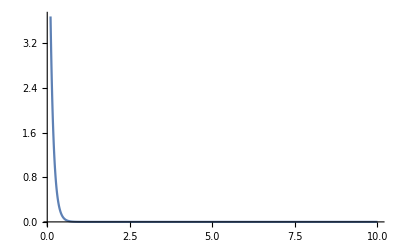

```mathematica
Plot[Exp[-δt / τ]/τ/.τ->0.1,{δt,0.1,10},PlotRange->All]
```

### Pure ohmic case: Unruh-Zurek

Pure ohmic (it’s unphysical because it has no cutoff): 
 -Graphics-

#### Master eq

-Graphics-

#### Coefficients

```mathematica
-Graphics-
-Graphics-
-Graphics-
-Graphics-
```

```mathematica
Series[Coth[β ω/2],{β,0,1}]
```

2/(ω β)+(ω β)/6+O[β]^2

```mathematica
Integrate[1/π ω 2/(ω β) Cos[ω t],{ω,0,Λ}]
Integrate[% Sin[Ω t]Exp[-γ t],t] 
Assuming[t>0&&Ω>0,Series[%,{Λ,∞,0}]//FullSimplify]
```

(2 Sin[t Λ])/(π t β)

1/(2 π β)(ExpIntegralEi[-t (γ-ⅈ (Λ-Ω))]+ExpIntegralEi[-t (γ+ⅈ (Λ-Ω))]-ExpIntegralEi[-t γ-ⅈ t (Λ+Ω)]-ExpIntegralEi[-t γ+ⅈ t (Λ+Ω)])

(ⅇ^(-ⅈ t Λ-t (γ-ⅈ Ω)+O[1/Λ]^2)+ⅇ^(-ⅈ t Λ-t (γ+ⅈ Ω)+O[1/Λ]^2)+ⅇ^(ⅈ t Λ-t (γ+ⅈ Ω)+O[1/Λ]^2)+ⅇ^(ⅈ t Λ+(-t γ+ⅈ t Ω)+O[1/Λ]^2)) O[1/Λ]^1

```mathematica
Exp[-ⅈ t Λ-t (γ-ⅈ Ω)]+Exp[-ⅈ t Λ-t (γ+ⅈ Ω)]+Exp[ⅈ t Λ-t (γ+ⅈ Ω)]+Exp[ⅈ t Λ-t (γ-ⅈ Ω)]//FullSimplify
```

4 ⅇ^(-t γ) Cos[t Λ] Cos[t Ω]

#### From Unruh-Zurek paper

-Graphics-
-Graphics-
-Graphics-

### Markovian case: Caldeira-Leggett (ohmic & at high T)

-Graphics-
From the original Caldeira-Leggett paper, at hight  T  limit:s
-Graphics-
It looks like there's one ħ discrepancy between Caldeira-Legget and the Hu-Path-Zhang paper. I guess Caldeira-Legget is correct, since it gives the right D in the classical limit.

### Wigner equation for the Markovian case, my derivation

The ħ in the diffusion term should be gone. This result is consistent with Caldeira-Leggett.

#### ∂/(∂ t)W(x,p,t)= (-∂/(∂ x){p}+∂/(∂ p){Ω^2 x+2 γ_0 p}+2 γ_0 k_B T ħ∂^2/(∂ p^2))W(x,p,t)

H =1/2 p^2+1/2 Ω^2 x^2
{H, W} =(∂ H)/(∂ x)(∂ W)/(∂ p)-(∂ H)/(∂ p) (∂ W)/(∂ x)=Ω^2 x(∂ W)/(∂ p)-p(∂ W)/(∂ x)

```mathematica
{ħ^2(-ⅈ/ħ),-Ω^2 x (- ⅈ ħ),-2ⅈ ħ γ (-1),-ⅈ 2 k T γ (-ħ^2)}/(ⅈ ħ)
```

{-1,x Ω^2,2 γ,2 ħ k T γ}

#### Langevin equations: ẋ=p ṗ=-2 γ_0 p -Ω^2 x+ξ(t)s

We set m=1

Fokker-Planck (Kramer’s equation):
-Graphics-
-Graphics-(α=γ)

#### ⅈ ħ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t) ={ħ^2∂^2/(∂ x∂ Δ)-Ω^2 x Δ-2ⅈ ħ γ_0 Δ∂/(∂ Δ)-ⅈ 2 k_B T γ_0 Δ^2}ρ_r(x-Δ/2,x+Δ/2,t)

Change of variables:
 y→ x-Δ/2, y'→ x+Δ/2
the inverse transformation is (looks like Keldysh rotation!):
x→ 1/2(y+y') ,Δ→ y'-y
ⅈ ħ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t) ={ħ^2∂^2/(∂ x∂ Δ)-Ω^2 x Δ-2ⅈ ħγ_0 Δ∂/(∂ Δ)-ⅈ 2 k_B Tγ_0 Δ^2}ρ_r(x-Δ/2,x+Δ/2,t)

y-y'=-Δ
y^2-y'^2=-2 x Δ
(y-y')^2=Δ^2
(∂/(∂ y)-∂/(∂ y'))ρ_r(y,y',t) =-2∂/(∂ Δ)ρ_r(y(x,Δ),y'(x,Δ),t)
(∂^2/(∂ y^2)-∂^2/(∂ y'^2))ρ_r(y,y',t) =-2∂^2/(∂ x∂ Δ)ρ_r(y(x,Δ),y'(x,Δ),t)

	∂/(∂ y)ρ_r(y,y',t)={(∂ x)/(∂ y)∂/(∂ x)+(∂ Δ)/(∂ y)∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
                                              ={1/2∂/(∂ x)-∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
	∂/(∂ y')ρ_r(y,y',t)={1/2∂/(∂ x)+∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
	∂^2/(∂ y^2)ρ_r(y,y',t)={1/2∂/(∂ x)-∂/(∂ Δ)}^2 ρ_r(y(x,Δ),y'(x,Δ),t)
              ∂^2/(∂ y'^2)ρ_r(y,y',t)={1/2∂/(∂ x)+∂/(∂ Δ)}^2 ρ_r(y(x,Δ),y'(x,Δ),t)

(∂/(∂ y)+∂/(∂ y'))ρ_r(y,y',t) =∂/(∂ x)ρ_r(y(x,Δ),y'(x,Δ),t)

```mathematica
{y-yp,y^2-yp^2,(y-yp)^2}/.{y-> (x-Δ/2),yp-> (x+Δ/2)}//FullSimplify
```

{-Δ,-2 x Δ,Δ^2}

#### ∂/(∂ Δ)→-ⅈ/ħ p, Δ→- ⅈ ħ ∂/(∂ p) , Δ∂/(∂ Δ)→- ∂/(∂ p) p, Δ^2→-ħ^2∂^2/(∂ p^2)

W(x,p,t)=∫ d Δ  exp(ⅈ/ħ p Δ)   ρ_r(x-Δ/2,x+Δ/2,t)
∂/(∂ t)W(x,p,t)=∫ d Δ  exp(ⅈ/ħ p Δ) ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t)
We can use the replaments:
exp(ⅈ/ħ p Δ)  Δ→  -ⅈ ħ∂/(∂ p)exp(ⅈ/ħ p Δ) 
	exp(ⅈ/ħ p Δ)  Δ^2→ -ħ^2∂^2/(∂ p^2)exp(ⅈ/ħ p Δ) 

∫ d Δ  exp(ⅈ/ħ p Δ)  Δ^2 ρ_r(x-Δ/2,x+Δ/2,t)=-ħ^2∂^2/(∂ p^2)W(x,p,t)
	
∫ d Δ  exp(ⅈ/ħ p Δ)   Δ∂/(∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)
		= -ⅈ ħ∂/(∂ p)∫ d Δ exp(ⅈ/ħ p Δ) ∂/(∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)
{integration by parts}
                          =ⅈ ħ∂/(∂ p)∫ d Δ ⅈ/ħ p exp(ⅈ/ħ p Δ) ρ_r(x-Δ/2,x+Δ/2,t)
		=- ∂/(∂ p) p W(x,p,t)
	
∫ d Δ  exp(ⅈ/ħ p Δ)   Δ ρ_r(x-Δ/2,x+Δ/2,t)= -ⅈ ħ ∂/(∂ p)W(x,p,t)
∫ d Δ  exp(ⅈ/ħ p Δ)  ∂^2/(∂ x∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)=-ⅈ/ħ p∂/(∂ x)W(x,p,t)

```mathematica
D[Exp[ⅈ/ħ p Δ],{p,1}]
D[Exp[ⅈ/ħ p Δ],{p,2}]
```

(ⅈ ⅇ^((ⅈ p Δ)/ħ) Δ)/ħ

-(ⅇ^((ⅈ p Δ)/ħ) Δ^2)/ħ^2

### Supraohmic high T, weak-coupling assumption (analytical result exists)

### Subohmic case?

## Nonlinear QBM

Particle:
-Graphics-
Harmonic oscillator bath:
-Graphics-
Interaction:
-Graphics-
	Linear coupling: k=1, f(x)=x
	Quadratic coupling: k=2
	Cubic coupling: k=3
	Quartic coupling: k=4

### Initial bath in thermal eq

-Graphics-
Hence the influence potential factorizes:
-Graphics-

### Perturbation theory, up to λ^2

F_n[x,x']=Exp{ⅈ/ħ δA_n[x,x']}
The influence action in small λ perturbation:
-Graphics-
where ⟨...⟩_0 is averaging over the bath action, without interaction.

### Quadratic case k=2

Vertex function
-Graphics-
Renormalized potential
-Graphics- 
-Graphics-

### Anharmonic case

-Graphics-
Counterterm:
-Graphics-

-Graphics-

-Graphics-
Typo: (∂ f(x'))/(∂ x')ẋ' 
Use standard approach analogous of deriving the wave function from the path integral (see also derivation in Caldeira-Leggett, page 605-607 ), we get: 

-Graphics-

-Graphics-
-Graphics-

Wigner function definition
-Graphics-
Wigner eq for the anharmonic case:
-Graphics-

```mathematica
Integrate[Exp[-a ξ^2+b ξ]ξ,{ξ,-∞,∞}]
```

ConditionalExpression[(b ⅇ^(b^2/(4 a)) √π)/(2 a^(3/2)), Re[a]>0]

### Semiclassical limit and FP for the anharmonic case

At the semiclassical limit, Wigner eq -> FP eq, 
∂/(∂ t)W = {V_ren,W}+2 γ_o X∂/(∂ p)(X p W)+2 k_B T γ_0 X^2∂^2/(∂ p^2)W
and the asymptotic solution is:
-Graphics-

{V_ren, W} =(∂ V_ren)/(∂ x)(∂ W)/(∂ p)-(∂ V_ren)/(∂ p) (∂ W)/(∂ x)
∂/(∂ p)(X p W)=X W+X p∂/(∂ p)W

∂/(∂ t)W(X,p,t)={ -(∂ V_ren)/(∂ p) ∂/(∂ X)+(∂ V_ren)/(∂ X)∂/(∂ p)+2 γ_o X^2∂/(∂ p)[p ·] +2 k_B T γ_0 X^2∂^2/(∂ p^2)}W(X,p,t)
I think V_ren(X)...

Compare with the one from the classical Brownian motion:
-Graphics-